# Στοχαστικες Μεταβλητες

Μια στοχαστικη μεταβλητη περιγράφει π.χ. το αποτελεσμα ενος παιχνιδιου τυχης, στο οποιο σε καθε εκτελεση του περνουμε και διαφορετικο αποτελεσμα.

Πυκνοτητα πιθανοτητας (PDF: Probability Density Function).
Επαναλαμβανουμε ενα τυχερο παιχνιδι πολλες φορες και δημιουργουμε ενα ιστογραμμα των αποτελεσματων του. Το ιστογραμμα αυτό αποδιδει τη πυκνοτητα πιθανοτητας της στοχαστικης μεταβλητης που περιγραφει το φαινομενο. Δηλαδη, P(x) είναι ο τρόπος κατανομής του x, που ονομάζεται πυκνοτητα πιθανοτητας της στοχαστικης μεταβλητής, η δε ποσοτητα P(x)dx δίνει τη πιθανοτητα (PDF) η μεταβλητη x να βρεθει στο διαστημα x→x+dx σε πειραμα προσδιορισμου της τιμης της.

Η ποσοτητα PDF προσδιοριζει πληρως μια στοχαστική μεταβλητη, απ' την οποία μπορουμε να βρούμε χαρακτηριστικες ποσοτητες της, όπως π.χ. τη μεση της τιμη μ, και τη διασπορα της σ^2, οι οποιες δινονται απο τις σχεσεις

		μ=<x>=∫P(x) xⅆx
σ^2 = <(δx)^2> =<(x-<x>)^2>=∫P(x) (x-<x>)^2 ⅆx

Σε πολλες ομως περιπτωσεις δεν γνωριζουμε τη PDF μιας στοχαστικης μεταβλητης. Έτσι προσπαθούμε να προσδιορισουμε τις παραμετρους της απο πειραματικα δεδομενα. Οι κύριες παράμετροι είναι η μέση τιμή, και η διασπορά της μεταβλητής.

Προσδιορισμος παραμετρων απο πειραματικα δεδομενα
Εκτελουμε το πειραμα ν φορες και προσδιοριζουμε τα αποτελέσματα του (δημιουργουμε δηλαδή μια συλλογή αποτελεσμάτων), δηλαδή τις τιμές της στοχαστικης μεταβλητης {x_1, x_2, x_3, ..., x_ν}. Απο τα αποτελεσματα αυτά προσπαθούμε να υπολογισουμε τις παραμετρους της κατανομης.

Προσδιορισμος της μεσης τιμης από τα αποτελέσματα των μετρησεων,
		<x> =μ ≃ (x_1+x_2+...+x_ν)/ν 

Προσδιορισμος της Τυπικης αποκλισης σ της μεταβλητής x γίνεται απο τη σχέση
		σ_x=√(1/(ν-1)∑_(i=1)^ν (x_i-<x>)^2)

## Μέση Μεταβλητή

Από τις πολλαπλές αυτές τυχαίες τιμές του x, δημιουργούμε μια συλλογή από τις τυχαίες μεταβλητές {x_i, i=1, 2, ...N}.  Κατόπιν ορίζουμε τη στοχαστική μεταβλητή X (μέση μεταβλητή της συλλογής) 
                                              X=1/N∑_(i=1)^N x_i, 

Από τη θεωρία έχουμε ότι
		<X>=<x>=μ
		
Το δε σφάλμα στη μεση τιμή ισουται με

		σ_X=σ_x/√Ν

Θέλουμε να επιβεβαιώσουμε τα αποτελέσματα αυτά.
Μπορούμε να επαναλάβουμε το σύνθετο αυτό πείραμα πολλές φορές.
Δηλαδή κάθε σύνθετο πείραμα αποτελείται από μια συλλογή απλών αποτελεσμάτων.

Σύμφωνα με τα γνωστά, προσδιορίζουμε μέση τιμή και διασπορά της μέσης μεταβλητής.
Κατόπιν υπολογίζουμε τις ίδιες ποσότητες με βάση τη θεωρία, και συγκρίνουμε τα δύο αποτελέσματα.

## Παραδειγμα

Εστω ότι τα πειραματικα αποτελεσματα μετρησεων μιας παραμετρου προσδιοριζονται απο τα αποτελεσματα της εντολής

```mathematica
measure:=Random[]-0.5
```

Οποτε εκτελούμε το "πειραμα" m φορές και εχουμε τις ακολουθες μετρησεις

```mathematica
m=1000;
```

```mathematica
data=Table[measure,{m}];
```

Που εχουν την εξης κατανομή

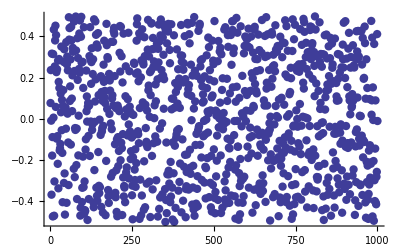

```mathematica
fig1=ListPlot[data,PlotStyle->{PointSize[0.015]}]
```

Η κατανομή των μετρησεων βρίσκεται παρακάτω:

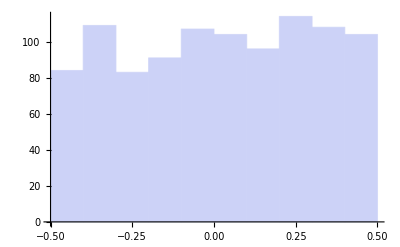

```mathematica
Histogram[data]
```

Οι παραμετροι που περιγραφουν τη στοχαστική αυτή μεταβλητή προσδιοριζονται παρακατω,

```mathematica
mx=Apply[Plus,data]/m
```

0.0181342

Η μεση τιμη προσδιοριζεται και με την ακολουθη εσωτερικη εντολη

```mathematica
Mean[data]
```

0.0181342

Τυπικη αποκλιση της στοχαστικής μεταβλητης ειναι

```mathematica
sx=Sqrt[Apply[Plus, (data-mx)^2]/(m-1)]
```

0.285506

Η οποια προσδιοριζεται και με τη χρηση της εσωτερικης εντολης

```mathematica
StandardDeviation[data]
```

0.285506

## Μεση μεταβλητη Συλλογης

Ενδιαφερομαστε  να βρουμε τιμές της "Μέσης τιμής", και το σφάλμα της.
Οριζουμε τη μέση μεταβλητη
Χ=(x_1+x_2+...+x_ν)/ν,

για m=ν.

Ακολουθει ο "Πειραματικος" προσδιορισμος της μέσης τιμής και του σφαλματος του Χ.

```mathematica
tX:=Sum[Random[]-0.5,{m}]/m
```

```mathematica
km=m
```

1000

Κανουμε km "μετρησεις" της ποσοτητας Χ

```mathematica
dataX=Table[tX,{km}];
```

Βρισκουμε τη κατανομη της

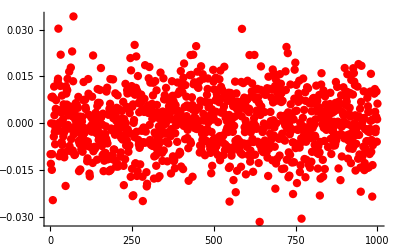

```mathematica
fig2=ListPlot[dataX,PlotStyle->{RGBColor[1,0,0],PointSize[0.015]}]
```

Κια υπολογιζουμε τη μεση τιμη και τη διασπορα της μεταβλητης αυτης

```mathematica
Mean[dataX]
```

0.0000132729

```mathematica
sX=StandardDeviation[dataX]
```

0.00928145

Απο τη θεωρια παίρνουμε οτι το σφαλμα στη μεταβλητη Χ=(x_1+x_2+...+x_ν)/ν ισουται με σ_Χ=σ_x/√ν. Οποτε μπορουμε να προσδιορισουμε απο το σφαλμα στο Χ, αυτο στο x,

```mathematica
sx/Sqrt[m]
```

0.0090285

Η διαφορετικη τιμή της τυπικης αποκλισης γινεται φανερη απο τα διαγραμματα fig1, fig2,

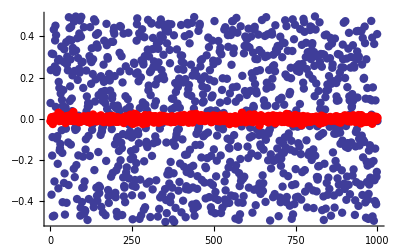

```mathematica
Show[fig1,fig2]
```

## Ασκηση (Directory: Random Variable)

Άσκηση 1. Να γίνει η παραπάνω ανάλυση, χρησιμοποιώντας ως τυχαίους αριθμούς αυτούς που παράγονται από τη κανονική κατανομή με μέση τιμή μηδέν και διασπορά ένα.